## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="ENO";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_ENO";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

{2pg,Null,Keq substrate}

{5.19,Keq value}

{2pg,Km or S05 substrate}

{0.0001,Km or S05 value}

{{{2pg,Null}},kcat substrates}

{330,kcat value}

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 330 | 313.5
346.5 | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 330 | 313.5
346.5 | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_ENO[c] + 2pg[c] <=> E_ENO[c]&2pg",
				"E_ENO[c]&2pg <=> E_ENO[c]&pep",
				"E_ENO[c]&pep <=> E_ENO[c] + pep[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(2pg)^c→0}

{pep^c→0}

{(2pg)^c→∞}

{pep^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/haldaneRatio_1.txt"	5.19
1	0.00001	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/relRateFor_2pg.txt"	0.9090909090909091
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/ENO/fit_ENO/input/absRateFor.txt"	330

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=50;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.491196028145
best_fit: 1.05502631465
best_fit: 0.429396879647
best_fit: 0.88967216627
best_fit: 1.01295310349
best_fit: 0.924089147351
best_fit: 0.949066394631
best_fit: 0.649053266962
best_fit: 0.737918831636
best_fit: 0.998752928668
best_fit: 0.993024027662
best_fit: 0.989534148487
best_fit: 0.994377909292
best_fit: 1.05322009211
best_fit: 1.01775502541
best_fit: 1.06937579535
best_fit: 0.734509169483
best_fit: 1.09491922048
best_fit: 0.464983549678
best_fit: 0.524431685845
best_fit: 1.0498345023
best_fit: 1.00785048766
best_fit: 1.02573545412
best_fit: 0.874278892346
best_fit: 0.883172825627
best_fit: 0.339675704395
best_fit: 0.818650037364
best_fit: 1.0969067778
best_fit: 0.880849553006
best_fit: 0.87114107024
best_fit: 1.01232080622
best_fit: 0.787472621132
best_fit: 0.628543766681
best_fit: 0.209673708707
best_fit: 0.935927176236
best_fit: 1.08348021336
best_fit: 0.604482176182
best_fit: 0.583447784729
best_fit: 0.623893410501
best_fit: 0.619658173877
best_fit: 0.262254825141
best_fit: 1.01596486131
best_fit: 0.421540330174
best_fit: 0.423409673855
best_fit: 0.97259773762
best_fit: 0.797757740961
best_fit: 0.969451116828
best_fit: 0.348256570159
best_fit: 0.316219612748
best_fit: 0.733629509163

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.1543×10^-11 | 1.33241×10^-22 | 1.37943×10^-10 | 2.65786×10^-9 | 5.19 | 5.19
1 | relRateFor_2pg | 2.19913×10^-12 | 4.83617×10^-24 | 4.60368×10^-13 | 5.06405×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_2pg | 2.08833×10^-12 | 4.36112×10^-24 | 6.57835×10^-13 | 4.80849×10^-10 | 0.136807 | 0.136807
1 | relRateFor_2pg | 1.93356×10^-12 | 3.73867×10^-24 | 8.93841×10^-13 | 4.45228×10^-10 | 0.20076 | 0.20076
1 | relRateFor_2pg | 1.73039×10^-12 | 2.99426×10^-24 | 1.13448×10^-12 | 3.98417×10^-10 | 0.284747 | 0.284747
1 | relRateFor_2pg | 1.48337×10^-12 | 2.20038×10^-24 | 1.32139×10^-12 | 3.41565×10^-10 | 0.386863 | 0.386863
1 | relRateFor_2pg | 1.20959×10^-12 | 1.4631×10^-24 | 1.39255×10^-12 | 2.78511×10^-10 | 0.5 | 0.5
1 | relRateFor_2pg | 9.3589×10^-13 | 8.75891×10^-25 | 1.32128×10^-12 | 2.15495×10^-10 | 0.613137 | 0.613137
1 | relRateFor_2pg | 6.88782×10^-13 | 4.74421×10^-25 | 1.13443×10^-12 | 1.58605×10^-10 | 0.715253 | 0.715253
1 | relRateFor_2pg | 4.8575×10^-13 | 2.35953×10^-25 | 8.93952×10^-13 | 1.1185×10^-10 | 0.79924 | 0.79924
1 | relRateFor_2pg | 3.31013×10^-13 | 1.0957×10^-25 | 6.57918×10^-13 | 7.62191×10^-11 | 0.863193 | 0.863193
1 | relRateFor_2pg | 2.19956×10^-13 | 4.83806×10^-26 | 4.60409×10^-13 | 5.0645×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.
1 | absRateFor | 4.53415×10^-13 | 2.05585×10^-25 | 3.44983×10^-10 | 1.0454×10^-10 | 330 | 330.

### Simulated Data and Best Fit Data Plot

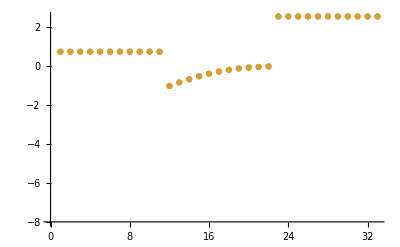

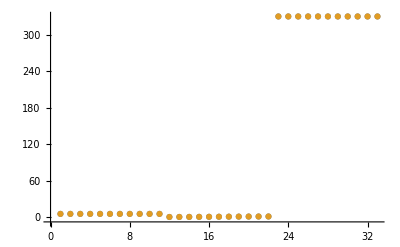

```mathematica
datasetI=20;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 2.51272×10^-6
0.00089 | 0.00089 | 1.39821×10^-6
0.00053 | 0.00053 | 1.35758×10^-6

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 3.33383×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 8.29398×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 4.57492×10^-6